```mathematica
$RecursionLimit = 100000
```

100000

```mathematica
inputFile = "Bav29.txt";
outputFile = "out_NonEff.txt";

hull = {};
SetDirectory["/Users/pinev/Documents/GitHub/UniversityPractices/Travelling salesman problem/wolfram"];
matrix = ReadList[inputFile, Real];
amtOfVertices = Floor[matrix[[1]]];
matrix = Delete[matrix,1];
matrix=Partition[matrix,2];
```

```mathematica
usedPath = Table[0, amtOfVertices];
(*allPathes = Table[Table[0, amtOfVertices], amtOfVertices]*)
allPathes = List[List[]];
pathes = Table[0, amtOfVertices];
```

```mathematica
matrix
```

{{1150.,1760.},{630.,1660.},{40.,2090.},{750.,1100.},{750.,2030.},{1030.,2070.},{1650.,650.},{1490.,1630.},{790.,2260.},{710.,1310.},{840.,550.},{1170.,2300.},{970.,1340.},{510.,700.},{750.,900.},{1280.,1200.},{230.,590.},{460.,860.},{1040.,950.},{590.,1390.},{830.,1770.},{490.,500.},{1840.,1240.},{1260.,1500.},{1280.,790.},{490.,2130.},{1460.,1420.},{1260.,1910.},{360.,1980.}}

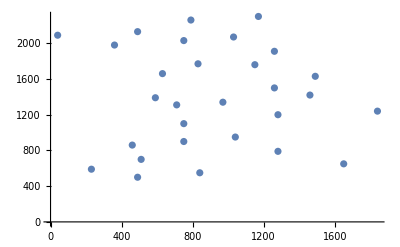

```mathematica
ListPlot[matrix]
```

```mathematica
matrix[[1, 1]]
```

1150.

```mathematica
route = Append[matrix,{matrix[[Length[matrix], 2]], matrix[[1, 1]]}]
```

{{1150.,1760.},{630.,1660.},{40.,2090.},{750.,1100.},{750.,2030.},{1030.,2070.},{1650.,650.},{1490.,1630.},{790.,2260.},{710.,1310.},{840.,550.},{1170.,2300.},{970.,1340.},{510.,700.},{750.,900.},{1280.,1200.},{230.,590.},{460.,860.},{1040.,950.},{590.,1390.},{830.,1770.},{490.,500.},{1840.,1240.},{1260.,1500.},{1280.,790.},{490.,2130.},{1460.,1420.},{1260.,1910.},{360.,1980.},{1980.,1150.}}

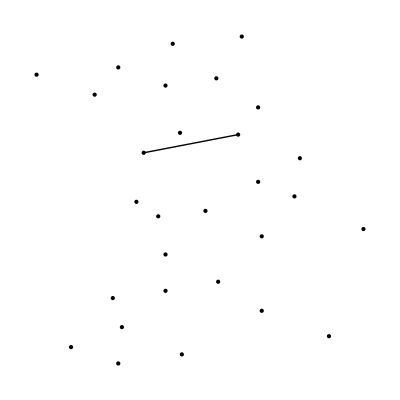

{{1150.,1760.},{630.,1660.},{40.,2090.},{750.,1100.},{750.,2030.},{1030.,2070.},{1650.,650.},{1490.,1630.},{790.,2260.},{710.,1310.},{840.,550.},{1170.,2300.},{970.,1340.},{510.,700.},{750.,900.},{1280.,1200.},{230.,590.},{460.,860.},{1040.,950.},{590.,1390.},{830.,1770.},{490.,500.},{1840.,1240.},{1260.,1500.},{1280.,790.},{490.,2130.},{1460.,1420.},{1260.,1910.},{360.,1980.}}

```mathematica
Graphics[{Point@matrix, Line[{{1150.,1760.},{630.,1660.}}]}]
matrix
```